## Models and Data Fitting

This notebook trys to verify the exponential technology evolution model.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
patentUSARaw=Import["USA-patent - Total patent grants (direct and PCT national phase entries)_Total count by filing office_1980_2014.csv"]

patentChinaRaw=Import["China-patent - Total patent grants (direct and PCT national phase entries)_Total count by filing office_1980_2014.csv"]
```

{{Intellectual property right :Patent},{},{Indicator :2 - Total patent grants (direct and PCT national phase entries)},{},{Source: WIPO statistics database. Last updated: December 2015},{},{,,,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014},{Office,Office (Code),Origin},{United States of America,US,Total,61827,65770,57889,56862,67201,71661,70860,82952,77924,95539,90366,96514,97443,98344,101676,101419,109646,111984,147520,153487,157496,166038,163518,169035,164291,143806,173770,157283,157772,167349,219614,224505,253155,277835,300678,}}

{{Intellectual property right :Patent},{},{Indicator :2 - Total patent grants (direct and PCT national phase entries)},{},{Source: WIPO statistics database. Last updated: December 2015},{},{,,,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014},{Office,Office (Code),Origin},{China,CN,Total,,,,,,44,56,422,1025,2303,,4122,3966,6556,3883,3393,2976,3494,4735,7637,13058,16296,21257,37154,49360,53305,57786,67948,93706,128389,135110,172113,217105,207688,233228,}}

```mathematica
patentUSARaw[[-1]]
patentUSARaw[[-3]]
patentChinaRaw[[-1]]
patentChinaRaw[[-3]]
patentUSARaw[[-3]]+patentChinaRaw[[-3]]
```

{United States of America,US,Total,61827,65770,57889,56862,67201,71661,70860,82952,77924,95539,90366,96514,97443,98344,101676,101419,109646,111984,147520,153487,157496,166038,163518,169035,164291,143806,173770,157283,157772,167349,219614,224505,253155,277835,300678,}

{,,,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014}

{China,CN,Total,,,,,,44,56,422,1025,2303,,4122,3966,6556,3883,3393,2976,3494,4735,7637,13058,16296,21257,37154,49360,53305,57786,67948,93706,128389,135110,172113,217105,207688,233228,}

{,,,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014}

{2 ,2 ,2 ,3960,3962,3964,3966,3968,3970,3972,3974,3976,3978,3980,3982,3984,3986,3988,3990,3992,3994,3996,3998,4000,4002,4004,4006,4008,4010,4012,4014,4016,4018,4020,4022,4024,4026,4028}

```mathematica
patentUSAYears=Delete[patentUSARaw[[-3]],{{1},{2},{3}}]-1980
Length@%
patentUSAAmounts=Delete[patentUSARaw[[-1]],{{1},{2},{3},{Length@patentUSARaw[[-1]]}}]
Length@%

patentChinaYears=
Drop[patentChinaRaw[[-3]],8]-1985
Length@%
patentChinaAmounts=ReplacePart[
Drop[
Delete[patentChinaRaw[[-1]],{{Length@patentChinaRaw[[-1]]}}]
,8]
,6->0]
Length@%
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34}

35

{61827,65770,57889,56862,67201,71661,70860,82952,77924,95539,90366,96514,97443,98344,101676,101419,109646,111984,147520,153487,157496,166038,163518,169035,164291,143806,173770,157283,157772,167349,219614,224505,253155,277835,300678}

35

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

30

{44,56,422,1025,2303,0,4122,3966,6556,3883,3393,2976,3494,4735,7637,13058,16296,21257,37154,49360,53305,57786,67948,93706,128389,135110,172113,217105,207688,233228}

30

```mathematica
patentUSAData=Transpose@Join[{patentUSAYears},{patentUSAAmounts}]
patentChinaData=
Transpose@Join[{patentChinaYears},{patentChinaAmounts}]
```

{{0,61827},{1,65770},{2,57889},{3,56862},{4,67201},{5,71661},{6,70860},{7,82952},{8,77924},{9,95539},{10,90366},{11,96514},{12,97443},{13,98344},{14,101676},{15,101419},{16,109646},{17,111984},{18,147520},{19,153487},{20,157496},{21,166038},{22,163518},{23,169035},{24,164291},{25,143806},{26,173770},{27,157283},{28,157772},{29,167349},{30,219614},{31,224505},{32,253155},{33,277835},{34,300678}}

{{0,44},{1,56},{2,422},{3,1025},{4,2303},{5,0},{6,4122},{7,3966},{8,6556},{9,3883},{10,3393},{11,2976},{12,3494},{13,4735},{14,7637},{15,13058},{16,16296},{17,21257},{18,37154},{19,49360},{20,53305},{21,57786},{22,67948},{23,93706},{24,128389},{25,135110},{26,172113},{27,217105},{28,207688},{29,233228}}

```mathematica
expModelUSAFit=FindFit[
patentUSAData,Exp[a t]+b ,{a,b},t
]
expModelChinaFit=FindFit[
patentChinaData,Exp[a t]+b,{a,b},t
]
(*expModelUSAChinaJointFit=FindFit[
patentUSAData+patentChinaData,Exp[a t]+b,{a,b},t
]
*)
```

{a→0.363597,b→112742.}

{a→0.432167,b→25262.6}

```mathematica
expModelUSAData=Table[{t,Exp[a t]+b /.expModelUSAFit},{t,0,34,1}]
expModelChinaData=Table[{t,Exp[a t]+b/.expModelChinaFit},{t,0,Length@patentChinaData-1,1}]
expModelChinaKernelData=Table[{t,Integrate[Exp[(t1)/2]a,{t1,-Infinity,t}]/.expModelChinaFit},{t,0,Length@patentChinaData-1,1}]
```

{{0,112743.},{1,112744.},{2,112744.},{3,112745.},{4,112747.},{5,112749.},{6,112751.},{7,112755.},{8,112761.},{9,112769.},{10,112780.},{11,112797.},{12,112821.},{13,112855.},{14,112905.},{15,112976.},{16,113079.},{17,113226.},{18,113438.},{19,113743.},{20,114182.},{21,114813.},{22,115721.},{23,117027.},{24,118905.},{25,121608.},{26,125495.},{27,131088.},{28,139132.},{29,150703.},{30,167349.},{31,191294.},{32,225738.},{33,275286.},{34,346561.}}

{{0,25263.6},{1,25264.1},{2,25265.},{3,25266.2},{4,25268.2},{5,25271.3},{6,25276.},{7,25283.2},{8,25294.3},{9,25311.5},{10,25337.9},{11,25378.6},{12,25441.3},{13,25538.},{14,25686.8},{15,25916.2},{16,26269.5},{17,26813.9},{18,27652.5},{19,28944.4},{20,30934.8},{21,34001.1},{22,38725.1},{23,46002.9},{24,57214.9},{25,74488.1},{26,101099.},{27,142096.},{28,205254.},{29,302557.}}

{{0,0.864333},{1,1.42504},{2,2.3495},{3,3.87367},{4,6.38661},{5,10.5297},{6,17.3606},{7,28.6228},{8,47.191},{9,77.8048},{10,128.278},{11,211.495},{12,348.697},{13,574.904},{14,947.857},{15,1562.75},{16,2576.54},{17,4248.},{18,7003.77},{19,11547.3},{20,19038.2},{21,31388.7},{22,51751.2},{23,85323.3},{24,140674.},{25,231933.},{26,382393.},{27,630459.},{28,1.03945×10^6},{29,1.71377×10^6}}

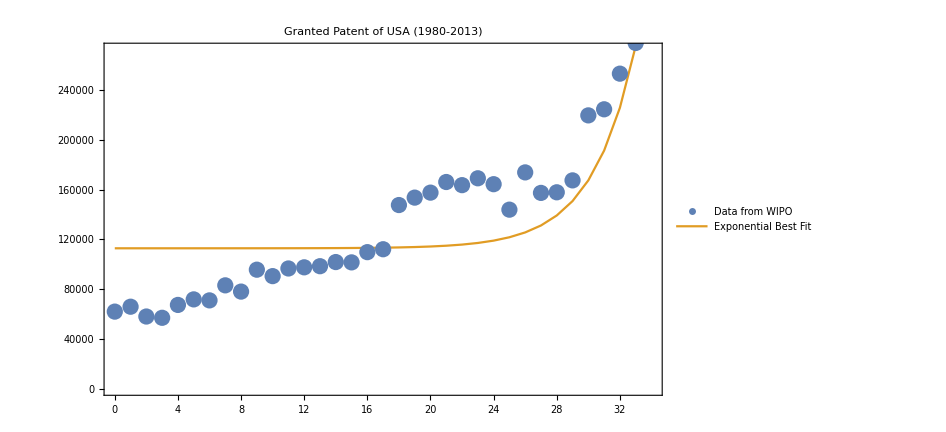

```mathematica
patentUSAPlt=ListPlot[
{patentUSAData,expModelUSAData},
Joined->{False, True},PlotLabel->"Granted Patent of USA (1980-2013)",Frame->True,ImageSize->700,PlotLegends->Placed[{"Data from WIPO","Exponential Best Fit"},{Center,Bottom}]
]
```

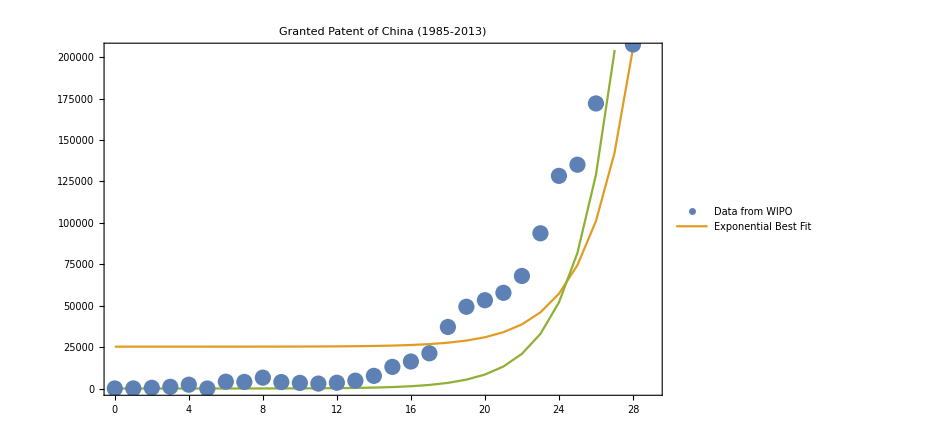

```mathematica
patentChinaPlt=ListPlot[
{patentChinaData,expModelChinaData,expModelChinaKernelData},
Joined->{False, True,True},PlotLabel->"Granted Patent of China (1985-2013)",Frame->True,ImageSize->700,PlotLegends->Placed[{"Data from WIPO","Exponential Best Fit"},{Center,Top}]
]
```

```mathematica
Export["patentUSAPlt.png",patentUSAPlt]
Export["patentChinaPlt.png",patentChinaPlt]
```

patentUSAPlt.png

patentChinaPlt.png

```mathematica
DSolve[
D[n[t],t]==c n[t],
n,t]
```

{{n→Function[{t},ⅇ^(c t) C[1]]}}